# Assignment 4

```mathematica
Needs["IGraphM`"]
```

## The configuration model

```mathematica
configurationModel[degrees_]:=With[{stubs=Catenate@MapIndexed[ConstantArray[First[#2],#1]&,degrees]},Graph[Range@Length[degrees],UndirectedEdge@@@Partition[RandomSample[stubs],2]]]
```

### Impossible graphs

```mathematica
configurationModel[{2,2}]
```

-Graphics-

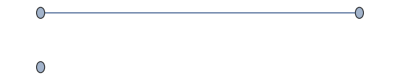

```mathematica
configurationModel[{1,1,1}]
```

```mathematica
SimpleGraphQ[%]
```

False

## Exploration of complexity in the configuration model

### Random graph (G(n,p))

```mathematica
d=Table[
Join[#,{n}]&/@Table[{m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, m/Binomial[n, 2]]]]]
,{k}
]],{m,1, 10, 1}]
, {n, {10, 20, 30,40, 50, 60}}];
ListPlot3D[Flatten[d,1],AxesLabel->{"m","p","n"},Ticks->{Automatic,Automatic,Automatic},Boxed->True,AxesStyle->Directive[Black,Thick],Mesh->All]
```

```mathematica
d=Table[{1-m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[5, 1-m]]]]
,{k}
]],{m,0,1, 0.1}]
```

{{1.,0.0108},{0.9,0.0218},{0.8,0.0491},{0.7,0.0946},{0.6,0.1685},{0.5,0.2902},{0.4,0.4291},{0.3,0.5905},{0.2,0.7717},{0.1,0.9252},{0.,1.}}

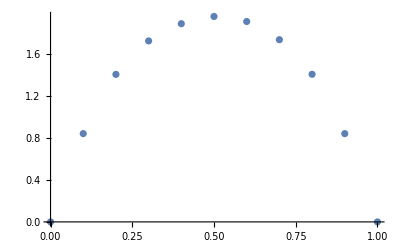

```mathematica
differences=Table[With[{degrees=VertexDegree[RandomGraph[BernoulliGraphDistribution[5, 1-m]]]},Max[degrees]-Min[degrees]],{m,0,1,0.1},{k,10000}  (*100 trials for each m*)];

averages=Mean/@differences;
Transpose[{Range[0,1,0.1],averages}];
ListPlot[%]
```

```mathematica
sparsities=Table[Module[{g,n,e,sparsity},g=RandomGraph[BernoulliGraphDistribution[5, 1-m]];
n=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(n (n-1));
sparsity],{m,0,1,0.1},{k,100}  (*100 trials per m*)];

averageSparsities=Mean/@sparsities;
```

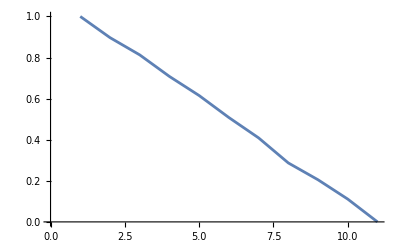

```mathematica
ListLinePlot[averageSparsities]
```

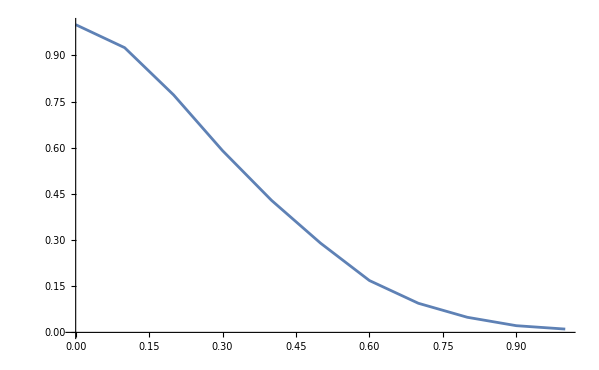

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{m,#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[50, m/Binomial[50,2]]];
Variance[VertexDegree[g]]
],{1000} ],{m,10,60, 3}];

d=N[%]
```

{{10.,0.39122},{13.,0.501711},{16.,0.615479},{19.,0.724841},{22.,0.849347},{25.,0.962519},{28.,1.05518},{31.,1.18388},{34.,1.29263},{37.,1.40278},{40.,1.5044},{43.,1.64771},{46.,1.72056},{49.,1.84424},{52.,1.97319},{55.,2.07137},{58.,2.14278}}

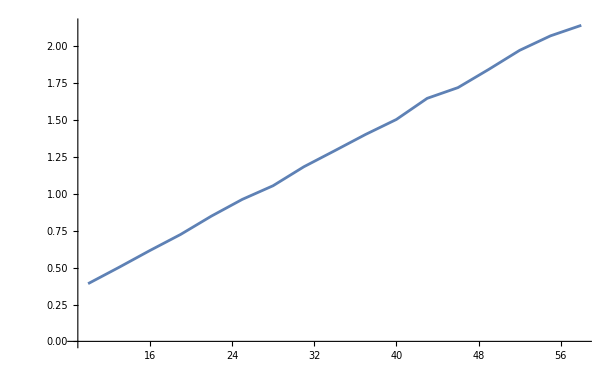

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n,2]]];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,1.34787},{13.,1.20603},{16.,1.10188},{19.,0.921175},{22.,0.833281},{25.,0.752337},{28.,0.684376},{31.,0.618204},{34.,0.558093},{37.,0.521722},{40.,0.477046},{43.,0.453773},{46.,0.416614},{49.,0.391827},{52.,0.372235},{55.,0.359987},{58.,0.341739}}

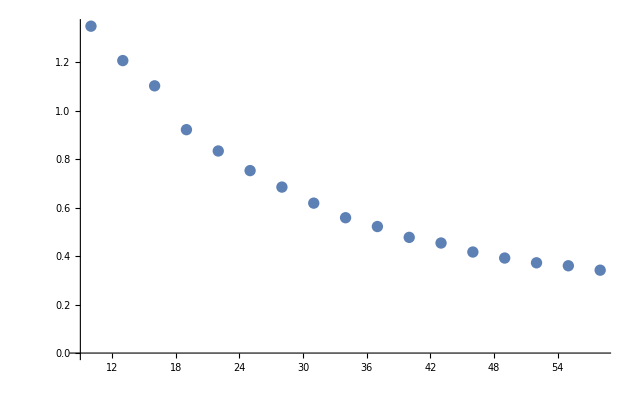

```mathematica
ListPlot[d]
```

### Star graph

```mathematica
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[Prepend[ConstantArray[1,m],m]]
,{k}
]],{m,1,15}]
```

{1.,0.6708,0.4011,0.2299,0.1246,0.066,0.0374,0.0179,0.0128,0.0053,0.003,0.0009,0.0011,0.0008,0.0004}

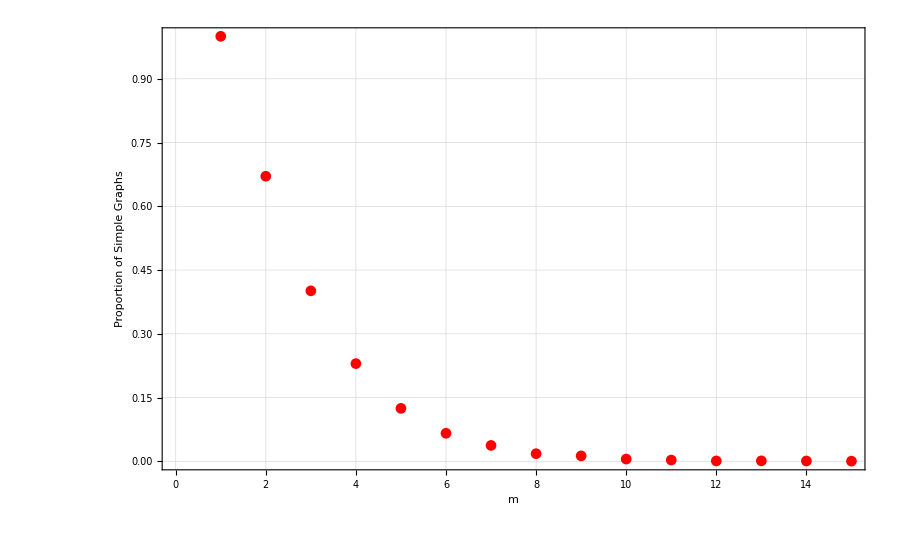

```mathematica
ListPlot[d,Frame->True,FrameLabel->{"m","Proportion of Simple Graphs"},PlotStyle->{Red,Thick},GridLines->Automatic,PlotMarkers->Automatic]
```

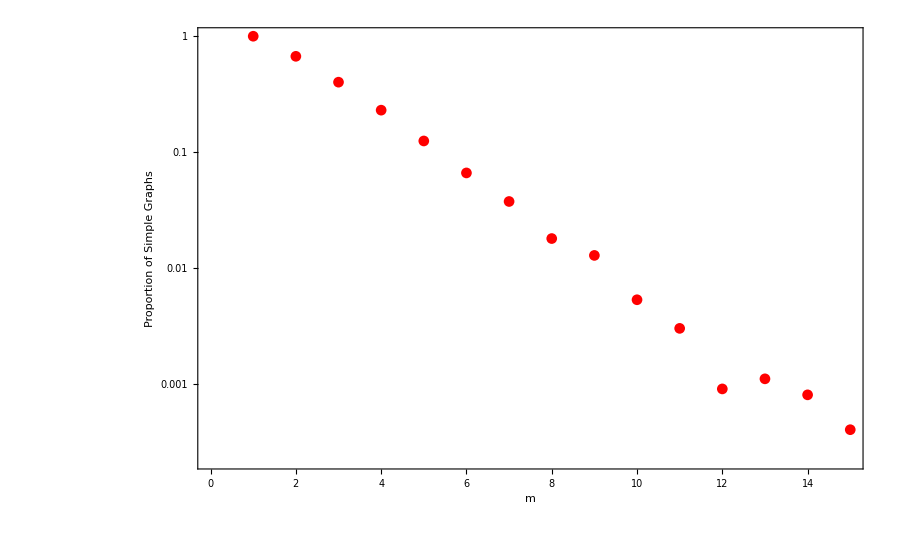

```mathematica
ListLogPlot[d,Frame->True,FrameLabel->{"m","Proportion of Simple Graphs"},PlotStyle->{Red,Thick},GridLines->Automatic,PlotMarkers->Automatic]
```

```mathematica
n=10;
da=Table[{m,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, m/Binomial[n, 2]]]]]
,{k}
]],{m,1, 10, 1}]
```

{{1,0.962},{2,0.8752},{3,0.7859},{4,0.668},{5,0.59},{6,0.4874},{7,0.4079},{8,0.3386},{9,0.2707},{10,0.2233}}

```mathematica
ListLinePlot[da,AxesLabel->{"m","p"}]
```

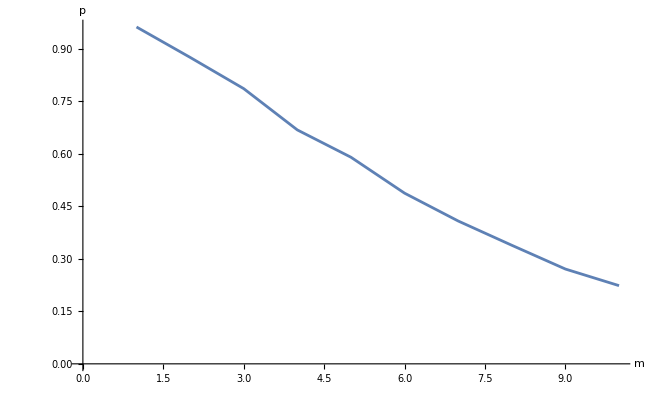

```mathematica
n=10;
da=Table[{n,N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]}&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n, 2]]]]]
,{k}
]],{n,10,60, 10}]
```

{{10,0.2129},{20,0.5255},{30,0.6783},{40,0.745},{50,0.7989},{60,0.8357}}

```mathematica
ListLinePlot[da,AxesLabel->{"n","p"}]
```

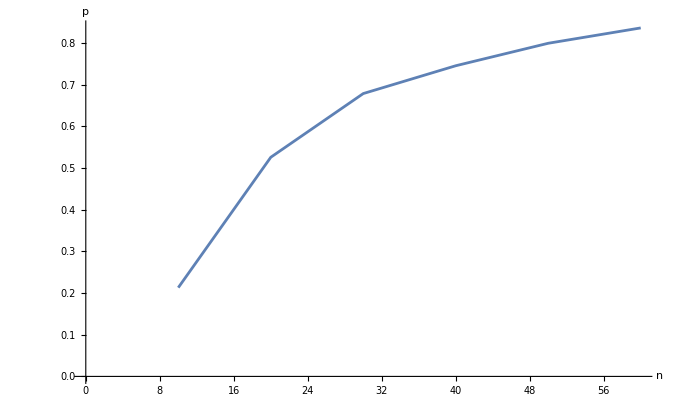

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[n, 10/Binomial[n,2]]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,493/2250},{13,503/3900},{16,9971/120000},{19,1973/34200},{22,1997/46200},{25,1243/37500},{28,10163/378000},{31,327/15500},{34,571/33000},{37,2021/133200},{40,9923/780000},{43,4969/451500},{46,833/86250},{49,9943/1176000},{52,379/51000},{55,248/37125},{58,3357/551000}}

{{10.,0.219111},{13.,0.128974},{16.,0.0830917},{19.,0.0576901},{22.,0.0432251},{25.,0.0331467},{28.,0.0268862},{31.,0.0210968},{34.,0.017303},{37.,0.0151727},{40.,0.0127218},{43.,0.0110055},{46.,0.00965797},{49.,0.00845493},{52.,0.00743137},{55.,0.00668013},{58.,0.00609256}}

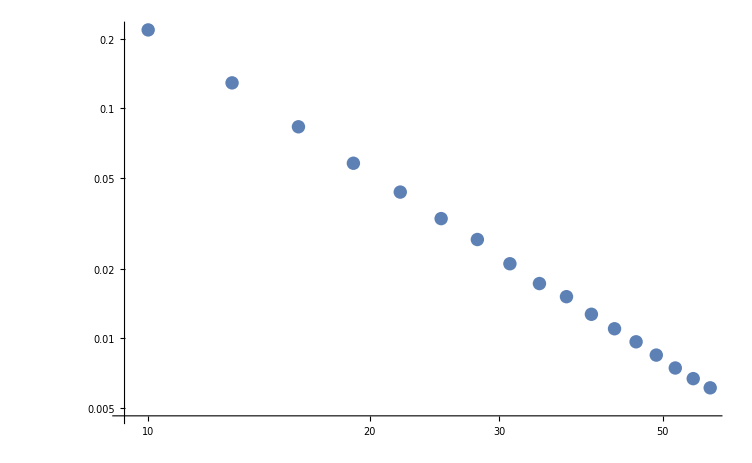

```mathematica
ListLogLogPlot[d]
```

```mathematica
Table[{m,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=RandomGraph[BernoulliGraphDistribution[50, m/Binomial[50,2]]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{m,10,60, 3}];

averageSparsities=Mean/@%
db=N[%]
```

{{10,407/49000},{13,2591/245000},{16,3167/245000},{19,9501/612500},{22,3147/175000},{25,24531/1225000},{28,28351/1225000},{31,223/8750},{34,8437/306250},{37,18483/612500},{40,20031/612500},{43,1079/30625},{46,11531/306250},{49,4917/122500},{52,5207/122500},{55,563/12500},{58,57851/1225000}}

{{10.,0.00830612},{13.,0.0105755},{16.,0.0129265},{19.,0.0155118},{22.,0.0179829},{25.,0.0200253},{28.,0.0231437},{31.,0.0254857},{34.,0.0275494},{37.,0.0301763},{40.,0.0327037},{43.,0.0352327},{46.,0.0376522},{49.,0.0401388},{52.,0.0425061},{55.,0.04504},{58.,0.0472253}}

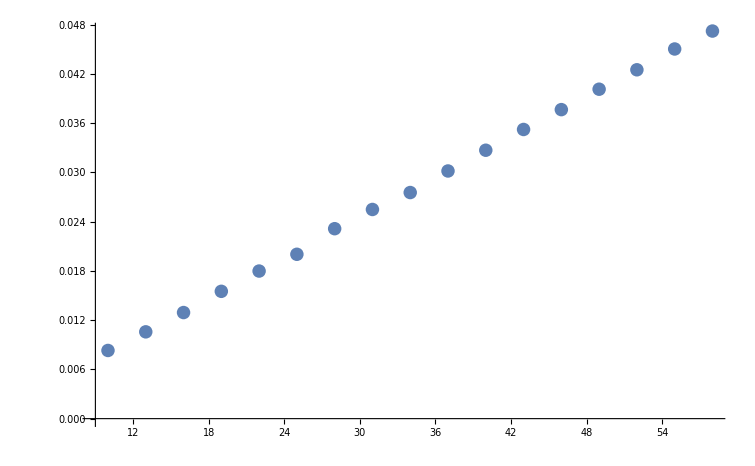

```mathematica
ListPlot[db]
```

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=StarGraph[n];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,1/5},{13,2/13},{16,1/8},{19,2/19},{22,1/11},{25,2/25},{28,1/14},{31,2/31},{34,1/17},{37,2/37},{40,1/20},{43,2/43},{46,1/23},{49,2/49},{52,1/26},{55,2/55},{58,1/29}}

{{10.,0.2},{13.,0.153846},{16.,0.125},{19.,0.105263},{22.,0.0909091},{25.,0.08},{28.,0.0714286},{31.,0.0645161},{34.,0.0588235},{37.,0.0540541},{40.,0.05},{43.,0.0465116},{46.,0.0434783},{49.,0.0408163},{52.,0.0384615},{55.,0.0363636},{58.,0.0344828}}

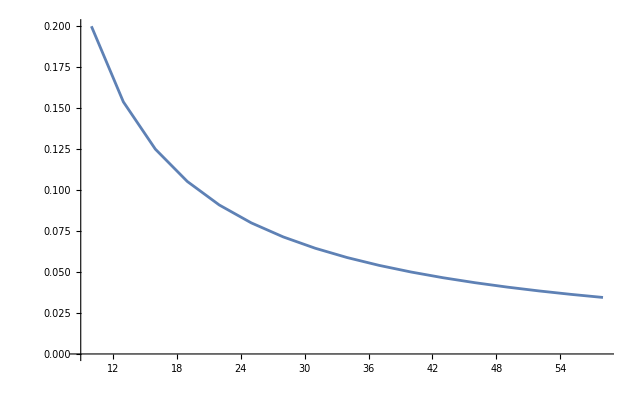

```mathematica
ListLinePlot[d]
```

```mathematica
k=10000;
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[StarGraph[m]]]
,{k}
]],{m,1,15}]
```

{1.,1.,0.6702,0.3969,0.2285,0.1234,0.0639,0.0374,0.0197,0.0105,0.0053,0.0031,0.0007,0.0007,0.0004}

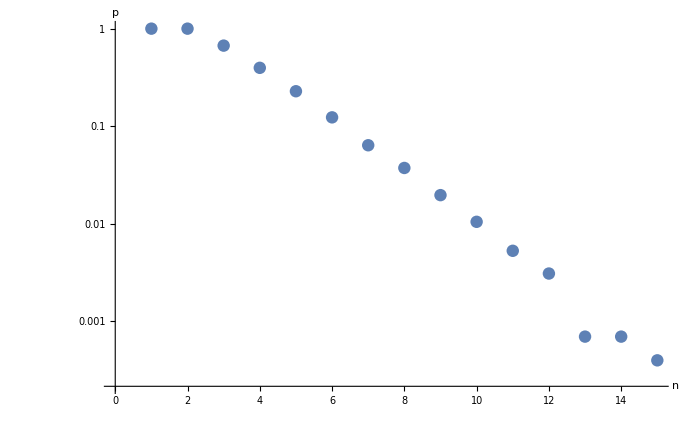

```mathematica
ListLogPlot[d,AxesLabel->{"n","p"}]
```

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=StarGraph[n];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,6.4},{13.,9.30769},{16.,12.25},{19.,15.2105},{22.,18.1818},{25.,21.16},{28.,24.1429},{31.,27.129},{34.,30.1176},{37.,33.1081},{40.,36.1},{43.,39.093},{46.,42.087},{49.,45.0816},{52.,48.0769},{55.,51.0727},{58.,54.069}}

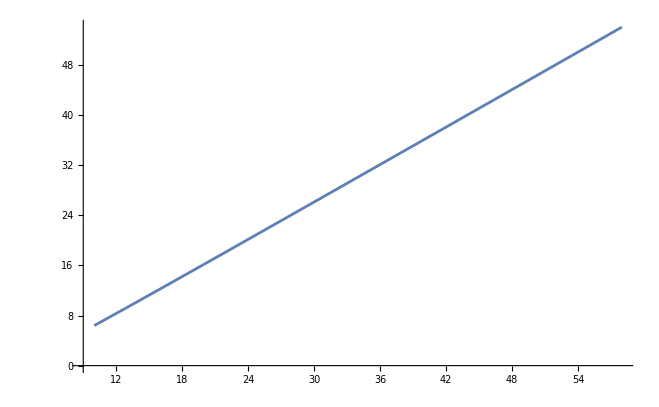

```mathematica
ListLinePlot[d]
```

### Barabási-Albert model

```mathematica
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]]
,{1000}
]],{m,1,15}]
```

{1.,1.,0.548,0.162,0.052,0.021,0.008,0.008,0.004,0.002,0.001,0.,0.001,0.001,0.}

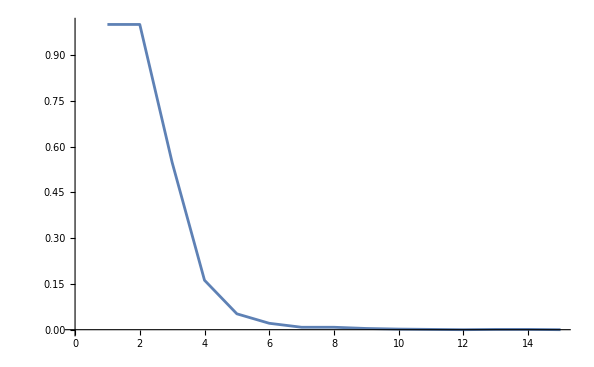

```mathematica
ListLinePlot[d]
```

```mathematica
Table[{n,Mean@@@#}&/@Table[Module[{g,v,e,sparsity},
g=UndirectedGraph[IGBarabasiAlbertGame[n,2]];
v=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(v (v-1));
sparsity
],{1000} ],{n,10,60, 3}];

averageSparsities=Mean/@%
d=N[%]
```

{{10,17/45},{13,23/78},{16,29/120},{19,35/171},{22,41/231},{25,47/300},{28,53/378},{31,59/465},{34,65/561},{37,71/666},{40,77/780},{43,83/903},{46,89/1035},{49,95/1176},{52,101/1326},{55,107/1485},{58,113/1653}}

{{10.,0.377778},{13.,0.294872},{16.,0.241667},{19.,0.204678},{22.,0.177489},{25.,0.156667},{28.,0.140212},{31.,0.126882},{34.,0.115865},{37.,0.106607},{40.,0.0987179},{43.,0.0919158},{46.,0.0859903},{49.,0.0807823},{52.,0.0761689},{55.,0.0720539},{58.,0.0683606}}

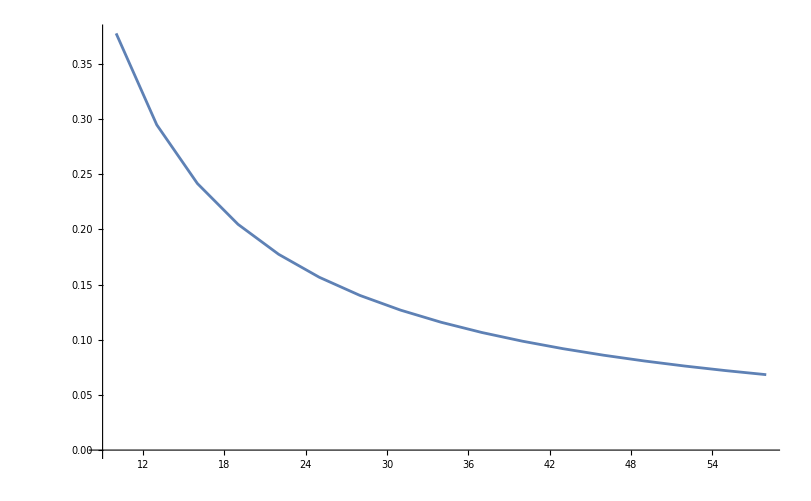

```mathematica
ListLinePlot[d]
```

```mathematica
Mean/@Table[{n,#}&/@Table[Module[{g,v,e,sparsity},
g=UndirectedGraph[IGBarabasiAlbertGame[n,2]];
Variance[VertexDegree[g]]
],{1000} ],{n,10,60, 3}];

d=N[%]
```

{{10.,4.032},{13.,5.75373},{16.,7.25467},{19.,8.70696},{22.,9.89408},{25.,11.2357},{28.,12.0865},{31.,12.7631},{34.,13.9469},{37.,14.965},{40.,15.7834},{43.,16.4471},{46.,17.6415},{49.,18.1297},{52.,18.9129},{55.,19.553},{58.,19.948}}

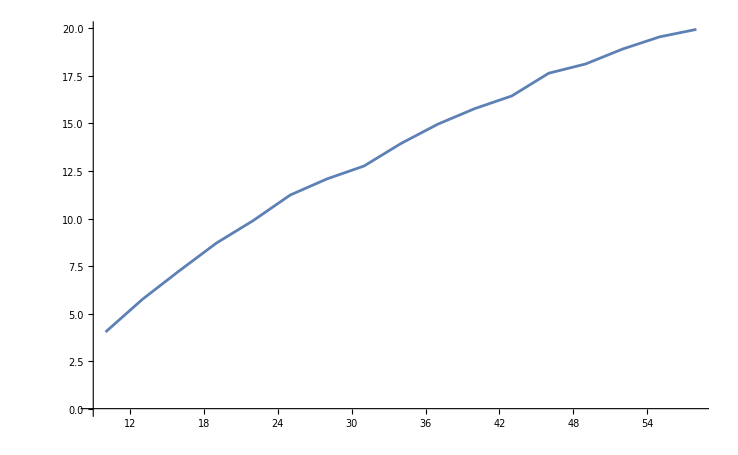

```mathematica
ListLinePlot[d]
```

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,1000}];

averages=Mean/@differences;
```

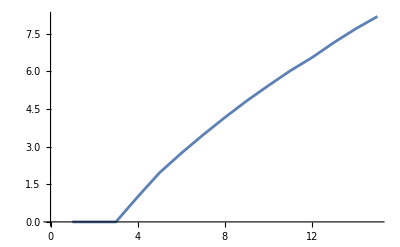

```mathematica
ListLinePlot[averages]
```

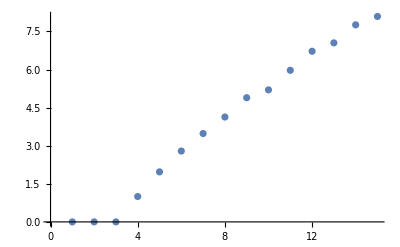

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,100}];

averages=Mean/@differences;
ListPlot[%]
```

```mathematica
d=Table[N[Lookup[#,True,0]/(Lookup[#,True,0]+Lookup[#,False,0])]&@Counts[SimpleGraphQ/@Table[
configurationModel[VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]]
,{k}
]],{m,1,15}]
```

```mathematica
differences=Table[With[{degrees=VertexDegree[UndirectedGraph[IGBarabasiAlbertGame[m,2]]]},Max[degrees]-Min[degrees]],{m,1,15},{k,1000}];

averages=Mean/@differences;
```

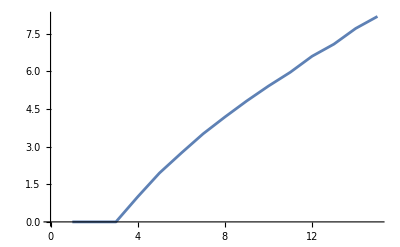

```mathematica
ListLinePlot[averages]
```

```mathematica
sparsities=Table[Module[{g,n,e,sparsity},g=UndirectedGraph[IGBarabasiAlbertGame[m,2]];
n=VertexCount[g];
e=EdgeCount[g];
sparsity=2 e/(n (n-1));
sparsity],{m,1,15},{k,100}  (*100 trials per m*)];

averageSparsities=Mean/@sparsities;
```

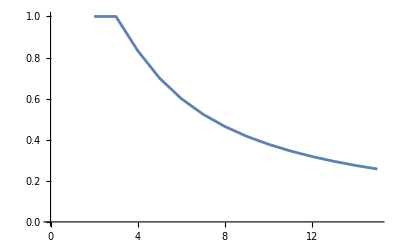

```mathematica
ListLinePlot[averageSparsities]
```

## Motifs February 10

```mathematica
Graph[#, ImageSize->40]&/@IGData[{"AllDirectedGraphs",3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
IGMotifs[RandomGraph[BernoulliGraphDistribution[100, 0.3]], 3]
```

{Indeterminate,Indeterminate,31312,4535}

```mathematica
networks=ExampleData/@Select[ExampleData["NetworkGraph"], StringStartsQ["Metabolic"]@*Last];
```

```mathematica
networks[[1]]
```

-Graphics-

```mathematica
configurationModel[VertexDegree[networks[[1]]]]
```

-Graphics-

```mathematica
IGMotifs[networks[[3]],3]
```

{Indeterminate,Indeterminate,11714,Indeterminate,24689,385,12788,0,0,432,11,0,0,0,0,0}

```mathematica
g=networks[[1]];
IGRewire[g, Floor[Length@VertexDegree[networks[[1]]]/3]]
```

-Graphics-

```mathematica
a=Table[IGMotifs[networks[[k]],3]/
(Mean/@N@Transpose[Table[IGMotifs[IGRewire[networks[[k]], Floor[Length@VertexDegree[networks[[k]]]]*4],3],{20}]]),{k, 1,Length[networks]}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
a//Dataset
```

```mathematica
Mean/@Transpose[a]
```

{Indeterminate,Indeterminate,1.16105,Indeterminate,1.16071,0.272965,1.15549,0.,0.,0.286471,0.432183,0.,0.,0.,0.,Indeterminate}

```mathematica
StandardDeviation/@Transpose[a]
```

{Indeterminate,Indeterminate,0.0209998,Indeterminate,0.0231511,0.0634136,0.0229079,0.,0.,0.0735344,0.966891,0.,0.,0.,0.,Indeterminate}

```mathematica
Max/@Transpose[a]
```

{Indeterminate,Indeterminate,1.20307,Indeterminate,1.21213,0.405268,1.20126,0.,0.,0.445869,6.25592,0.,0.,0.,0.,Indeterminate}

```mathematica
Min/@Transpose[a]
```

{Indeterminate,Indeterminate,1.08852,Indeterminate,1.08742,0.122299,1.06574,0.,0.,0.133205,0.0408476,0.,0.,0.,0.,Indeterminate}

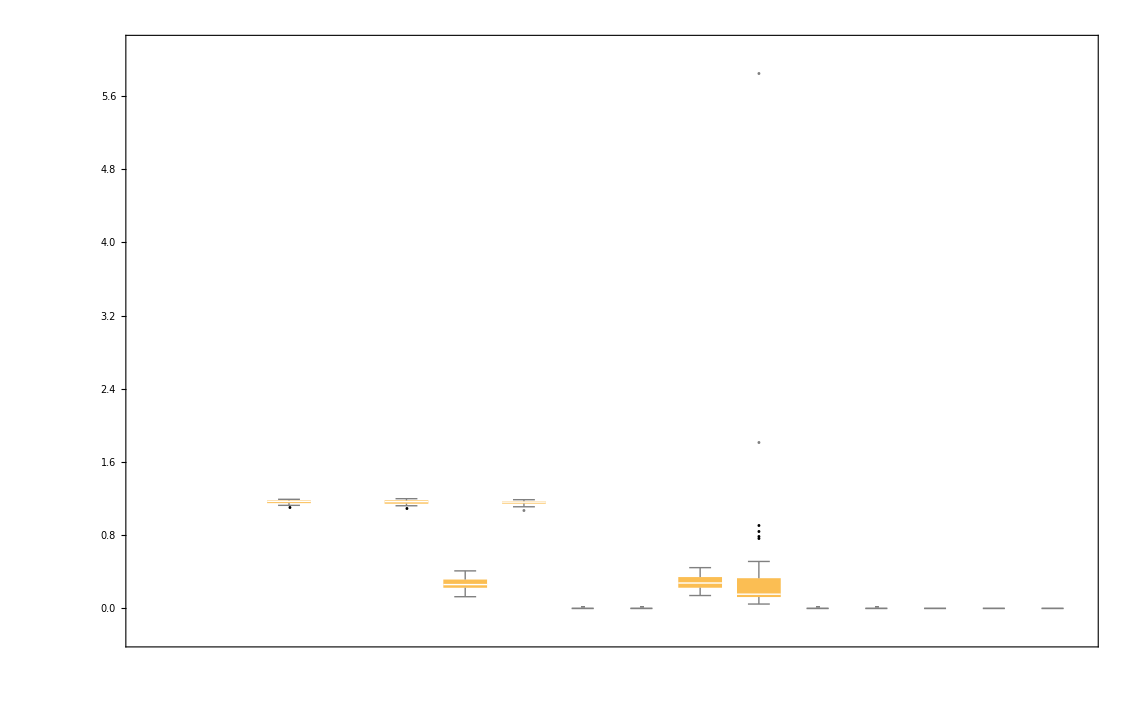

```mathematica
BoxWhiskerChart[Transpose[a],"Outliers",ChartLabels->(Graph[#]&)/@IGData[{"AllDirectedGraphs",3}],LabelingSize->40]
```

## GotGraphs Exploration

```mathematica
gotGraphs = Table[Module[{data},
data = Import["https://raw.githubusercontent.com/mathbeveridge/gameofthrones/refs/heads/master/data/got-s" <> ToString[k] <>"-edges.csv","CSV",HeaderLines->1];
Graph[
UndirectedEdge@@@data[[All,{1,2}]],
EdgeWeight->data[[All,3]],
VertexLabels->Automatic
]
],{k, 1, 8}];
```

### Initial Exploration

```mathematica
ListPlot[
{Length/@VertexList/@gotGraphs,
Length/@EdgeList/@gotGraphs,
0.1Total/@IGVertexStrength/@gotGraphs},
 Joined->True,
PlotLabels->{"nr. vertices","nr. Edges","strength"}
]
```

-Graphics-

### Nicer visualization

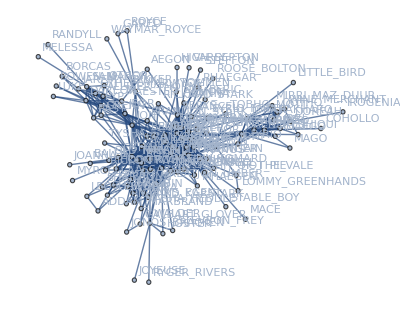

```mathematica
g=gotGraphs[[1]]
```

```mathematica
Table[Module[{g,edges,weights,logWeights,normalizedWeights,edgeStyles,vd,vl},
g=gotGraphs[[k]];
edges=EdgeList[g];
weights=PropertyValue[{g,#},EdgeWeight]&/@edges;

logWeights=Log10[weights+1]; 

normalizedWeights=Rescale[logWeights,{Min[logWeights],Max[logWeights]},{0.1,1}];

edgeStyles=Thread[edges->(Opacity[#]&/@normalizedWeights)];

vd=Thread[VertexList[g]->Normalize[VertexDegree[g],Total]*20];
vl=Thread[VertexList[g]->MapThread[Style[#1,FontSize->5+#2]&,{VertexList[g],Normalize[VertexDegree[g],Max]*20}]];

Graph[g,PlotTheme->"Monochrome",VertexSize->vd,VertexLabels->vl,EdgeStyle->edgeStyles,ImageSize->{1300,800}]

],{k,1,Length[gotGraphs]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Motifs GotGraph

```mathematica
a=Table[IGMotifs[SimpleGraph[gotGraphs[[k]]],3]/
(Mean/@N@Transpose[Table[IGMotifs[IGRewire[SimpleGraph[gotGraphs[[k]]], Floor[Length@VertexDegree[SimpleGraph[gotGraphs[[k]]]]]*4],3],{20}]]),{k, 1,Length[gotGraphs]}];
```

```mathematica
a//Dataset
```

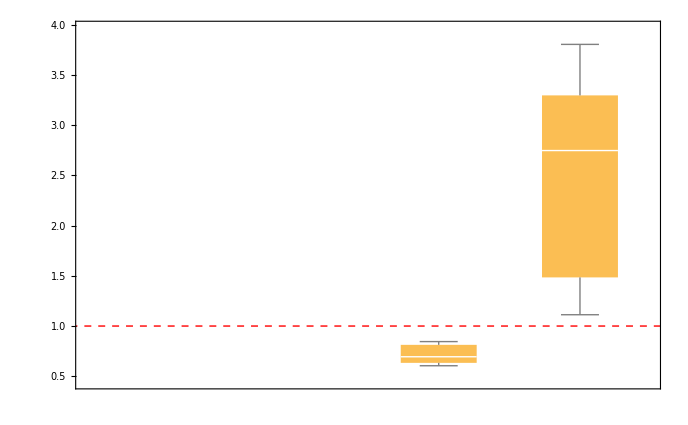

```mathematica
BoxWhiskerChart[Transpose[a],"Outliers",ChartLabels->(Graph[#]&)/@IGData[{"AllDirectedGraphs",3}],LabelingSize->40,Epilog->{Red,Dashed,Line[{{0,1},{Length[a]+1,1}}]}]
```

```mathematica
ListPlot[Log2/@{a[[All,4]],a[[All, 3]]},Joined->True,PlotLabels->{"Triangles","Wedges"}]
```

-Graphics-

### Motifs Real - world Graphs

```mathematica
networks=Table[ExampleData[{"NetworkGraph",e}],{e,{"ExpandedMovies","JazzMusicians","DolphinSocialNetwork","ZacharyKarateClub","September11Terrorists","URVEmailNetwork"}}];
```

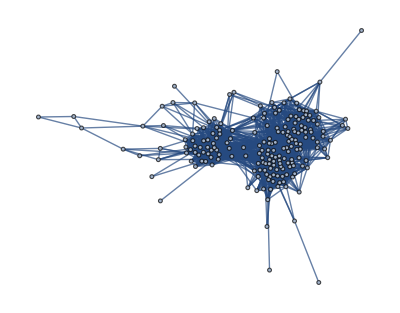
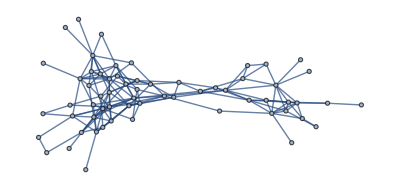
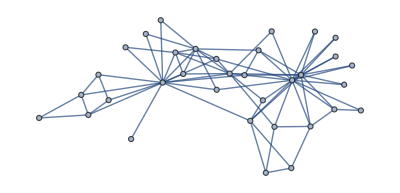
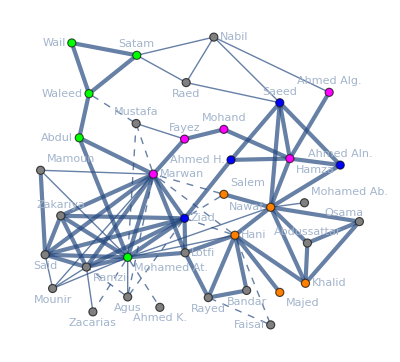
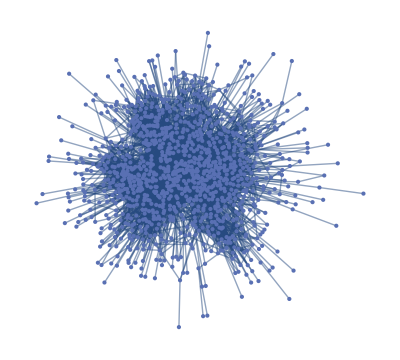
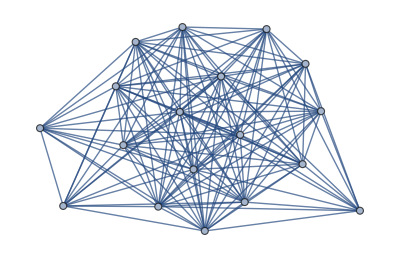

```mathematica
AppendTo[networks,IGBipartiteProjections[ExampleData[{"NetworkGraph","DavisSouthernWomen"}]][[1]]]
```

```mathematica
a=Table[IGMotifs[UndirectedGraph[networks[[k]]],3]/
(Mean/@N@Transpose[Table[IGMotifs[IGRewire[UndirectedGraph[networks[[k]]], Floor[Length@VertexDegree[UndirectedGraph[networks[[k]]]]]*4],3],{20}]]),{k, 1,Length[networks]}]//Dataset
```

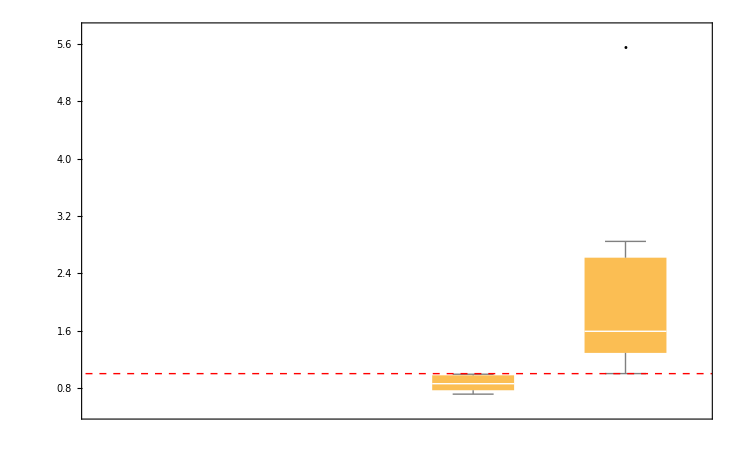

```mathematica
BoxWhiskerChart[Transpose[a],"Outliers",ChartLabels->(Graph[#]&)/@IGData[{"AllDirectedGraphs",3}],LabelingSize->40,Epilog->{Red,Dashed,Line[{{0,1},{Length[a]+1,1}}]}]
```

### Community structure

```mathematica
Table[Module[{graph=gotGraphs[[i]],communities},
communities=IGCommunitiesOptimalModularity[graph];
{
IGModularity[graph,communities],
CommunityGraphPlot[graph,communities["Communities"]] 
}
],{i,1,8}
]
```

{{0.529139,-Graphics-},{0.69668,-Graphics-},{0.757601,-Graphics-},{0.675006,-Graphics-},{0.74983,-Graphics-},{0.7243,-Graphics-},{0.449842,-Graphics-},{0.209911,-Graphics-}}

### Global Clustering Coefficient

```mathematica
ListPlot[IGGlobalClusteringCoefficient[gotGraphs[[#]]]&/@Range[1,8],Joined->True,PlotLabels->{"Global Clustering Coefficent"}]
```

-Graphics-

### Core-periphery structure

Evident from the nicer graph visualizations -> we don’t measure it really

### Centrality measures

```mathematica
g=gotGraphs[[1]];
edges=EdgeList[g];
weights=PropertyValue[{g,#},EdgeWeight]&/@edges;

logWeights=Log10[weights+1]; 

normalizedWeights=Rescale[logWeights,{Min[logWeights],Max[logWeights]},{0.1,1}];

edgeStyles=Thread[edges->(Opacity[#]&/@normalizedWeights)];

vd=Thread[VertexList[g]->Normalize[VertexDegree[g],Total]*20];
vl=Thread[VertexList[g]->MapThread[Style[#1,FontSize->5+#2]&,{VertexList[g],Normalize[VertexDegree[g],Max]*20}]];

Graph[g,PlotTheme->"Monochrome",VertexSize->vd,VertexLabels->vl,EdgeStyle->edgeStyles,ImageSize->{1300,800}]
```

-Graphics-

### Centralities

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-DegreeCentrality[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of degree centrality per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGVertexStrength[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of vertex strength per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Graph[gotGraphs[[1]],EdgeWeight->1/PropertyValue[gotGraphs[[1]],EdgeWeight]]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGBetweenness[Graph[gotGraphs[[k]],EdgeWeight->1/PropertyValue[gotGraphs[[k]],EdgeWeight]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Weighted Betweenness centrality (with adjusted weights) per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGBetweenness[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Betweenness per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGBetweenness@IGUnweighted[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Harmonic centrality per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

An interesting way to look at the most important characters in a smaller context -> look at the betweenness with a cutoff.

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGBetweennessCutoff[gotGraphs[[k]],5]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Betweenness per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-IGHarmonicCentrality[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Harmonic centrality per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-PageRankCentrality[gotGraphs[[k]]]}], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of Harmonic centrality per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
d=Table[
First[#]&/@Take[SortBy[Transpose[{VertexList[gotGraphs[[k]]],-Normalize[KatzCentrality[gotGraphs[[k]],0.85/Max[Eigenvalues[AdjacencyMatrix[gotGraphs[[k]]]]]],Total]}], Last],15]
, {k, 1, 8}
];
```

```mathematica
Dataset[{{"Top 15 characters by measure of Katz centrality per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, d]]]]}}]
```

### The isolated and the inbetweeners

Lost the code for this section, might reinvent it later

```mathematica
Table[
First[#]&/@Take[SortBy[Select[Transpose[{VertexList[gotGraphs[[k]]],IGLocalClusteringCoefficient[gotGraphs[[k]]]}],And[Less[#[[2]],1],Greater[#[[2]],0]]&], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of LocalClusteringCoefficient (inbetweener) per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

```mathematica
Table[
First[#]&/@Take[SortBy[Select[Transpose[{VertexList[gotGraphs[[k]]],-IGLocalClusteringCoefficient[gotGraphs[[k]]]}],And[Less[#[[2]],0],Greater[#[[2]],-1]]&], Last],15]
, {k, 1, 8}
];
Dataset[{{"Top 15 characters by measure of LocalClusteringCoefficient (Isolated) per season"}, {Dataset[Join[{Range[0,Length[%]]},Transpose[Join[{Range[1, Length[%[[1]]]]}, %]]]]}}]
```

### Edge removal experimentations

This is a lot of code, I’ll skip having the complete thing here

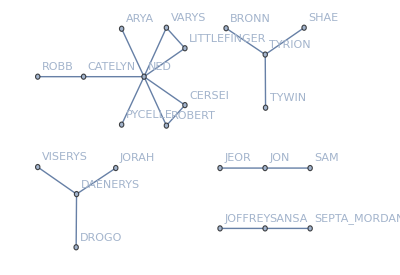

```mathematica
s=1;
PropertyValue[{gotGraphs[[s]],EdgeList[gotGraphs[[s]]]},EdgeWeight];
Graph[
Take[
SortBy[
EdgeList[gotGraphs[[s]]],
-PropertyValue[{gotGraphs[[s]],#},EdgeWeight]&],20
],
VertexLabels->"Name"
]
```

#### Thinking up our own metric of importance for an edge

Same here with the complete thing, but here’s a look

{DAENERYS<->JORAH,NED<->ROBERT,JON<->SAM,LORAS<->RENLY,BRONN<->TYRION,SHAE<->TYRION,SANSA<->SEPTA_MORDANE,ARYA<->SYRIO_FOREL,HOT_PIE<->LOMMY_GREENHANDS,DAENERYS<->DROGO,LITTLEFINGER<->VARYS,CATELYN<->ROBB,LITTLEFINGER<->NED,BRAN<->MAESTER_LUWIN,NED<->VARYS,JEOR<->JON,LYSA<->ROBIN,TYRION<->TYWIN,ROS<->THEON,GRENN<->PYP,CERSEI<->ROBERT,ROBB<->THEON,JOFFREY<->SANSA,CATELYN<->WALDER,WAYMAR_ROYCE<->WILL,ARYA<->NED,NED<->PYCELLE,MORD<->TYRION,GARED<->ROYCE,GREATJON_UMBER<->ROBB,CERSEI<->NED,DAENERYS<->MIRRI_MAZ_DUUR,DAENERYS<->VISERYS,CERSEI<->JOFFREY,JORY_CASSEL<->NED,ADDAM_MARBRAND<->LEO_LEFFORD,ARYA<->SANSA,JORAH<->RAKHARO,DOREAH<->VISERYS,JAIME<->TYWIN,SHAGGA<->TYRION,BENJEN<->JON,BRAN<->OSHA,BRAN<->ROBB,ILLYRIO<->VISERYS,JON<->MAESTER_AEMON,JON<->PYP,CERSEI<->JAIME,OSHA<->THEON,DAENERYS<->IRRI,JAIME<->JORY_CASSEL,JORAH<->VISERYS,GARED<->WILL,ROYCE<->WILL,BRAN<->RICKON,DAENERYS<->DOREAH,CATELYN<->RODRIK,AERYS<->RHAEGAR,PYP<->SAM,RYGER_RIVERS<->WALDER,LANCEL<->ROBERT,CATELYN<->LYSA,DAENERYS<->QOTHO,CATELYN<->NED,JAIME<->NED,AERYS<->RICKARD_STARK,ARYA<->STABLE_BOY,LYSA<->TYRION,JOFFREY<->MARILLION,KEVAN<->TYWIN,MIRRI_MAZ_DUUR<->QOTHO,GALBART_GLOVER<->JONOS_BRACKEN,RENLY<->ROBERT,STEVRON_FREY<->WALDER,RENLY<->STANNIS,BARRISTAN<->ROBERT,DROGO<->MAGO,MERYN_TRANT<->SYRIO_FOREL,GENDRY<->TOBHO_MOTT,BRAN<->HODOR,DAENERYS<->WINE_MERCHANT,TYRION<->YOREN,ARYA<->YOREN,DROGO<->VISERYS,BORCAS<->DAREON,BOWEN_MARSH<->DAREON,DAREON<->LUKE,BRAN<->OLD_NAN,ALLISER_THORNE<->SAM,CATELYN<->MAESTER_LUWIN,CERSEI<->SANSA,JOFFREY<->MYCAH,IRRI<->RAKHARO,NED<->SANSA,AEGON<->AERYS,GRENN<->JON,BARRISTAN<->NED,JON<->TYRION,PYP<->RAST,ALLISER_THORNE<->JON}

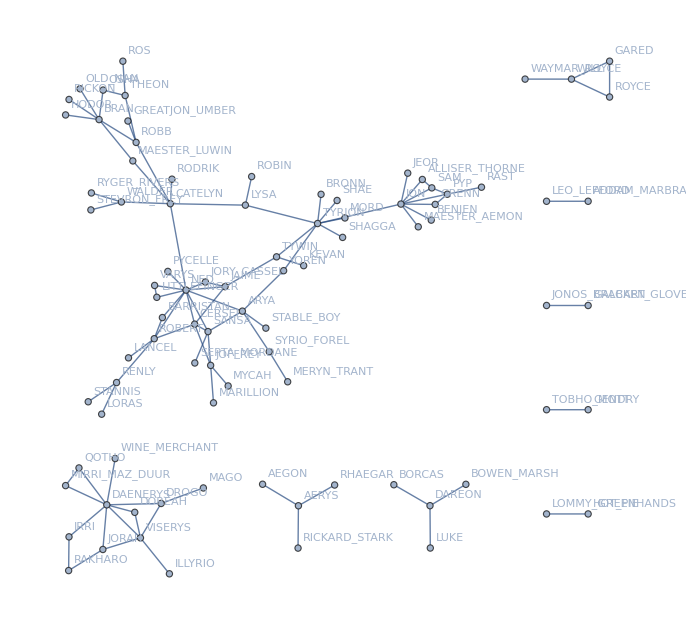

```mathematica
g = gotGraphs[[1]];
vertexStrength[v_]:=Total[PropertyValue[{g,#},EdgeWeight]&/@Select[EdgeList[g],MemberQ[List@@#,v]&]];
totalDeg=Total[VertexDegree[g]];

(*Compute a list of associations for each edge*)
edgeScores=Map[Function[edge,With[{a=First[edge],b=Last[edge],w=PropertyValue[{g,edge},EdgeWeight]},<|"Edge"->edge,"Score"->w^2/(vertexStrength[a]*vertexStrength[b])*(VertexDegree[g,a]+VertexDegree[g,b])/totalDeg|>]],EdgeList[g]];

(*Sort by descending score and take the top 10*)
sortedEdges=Take[SortBy[edgeScores,-#"Score"&],100];

(*If you want to extract just the edges from these associations:*)
extractedEdges=sortedEdges[[All,"Edge"]]

a=Graph[extractedEdges, VertexLabels->"Name", EdgeWeight->sortedEdges[[All,"Score"]]]
Dataset[ReverseSortBy[Transpose[{VertexList[a],VertexDegree[a]}], Last]]
Dataset[ReverseSortBy[Transpose[{VertexList[a],IGVertexStrength[a]}], Last]]
```